# How Fair is Monopoly? & Monopoly Revisited

## by Ian Stewart

Modelización del Monopoly estudiando Cadenas de Markov

José Luis Cánovas Sánchez

# How Fair is Monopoly?

Versión más básica del Monopoly, sin reglas de cuándo ir a la cárcel.

### ¿Cadena de Markov?

Llamamos X_n a la variable aleatoria que indica la casilla donde estamos tras la tirada n-ésima.
Veamos que (X_n) es una Cadena de Markov Homogénea.

Probabilidad de que la siguiente tirada caiga en la casilla j, siendo las anteriores (i_o,..., i_(n-1), i):
P[X_(n+1)=j|X_0=i_0,...,X_(n-1)=i_(n-1), X_n=i]
La siguiente casilla sólo depende de la actual y el valor de los dados lanzados:
P[X_(n+1)=j|X_n=i]
Como sólo depende de la n anterior, es Cadena de Markov
Además, el acabar en la casilla j partiendo de la i es independiente de si ocurre en la tirada 0 ó n+1:
P[X_(n+1)=j|X_n=i] = P[X_1=j|X_0=i]=p_ij
Por lo tanto, es Homogénea.

Considerando un el lanzamiento de un sólo dado, simulando tiradas fantasma, tenemos que:
	p_ij = 1/6, 	si  1 ⩽ (j-i) mod 40 ⩽ 6
	0 en el resto

-Graphics-

#### Matriz de Transición de la cadena de Markov: 1 dado

```mathematica
( M = Table[ If[  1 <= Mod[j-i, 40]  ≤ 6,1/6, 0] , {i,40},{j,40}] ) // MatrixForm
```

(0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6
1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6
1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Matriz de Transición de la cadena de Markov: 2 dados

También podemos trabajar directamente con M^2,  la matriz de transición de lanzar dos dados.

```mathematica
M2 = MatrixPower[M,2] ; M2 [[1]]
```

{0,0,1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Concuerda con las probabilidades del artículo, donde el 7 tiene la mayor probabilidad, 1/6, y los extremos (2 y 12) sólo 1/36.

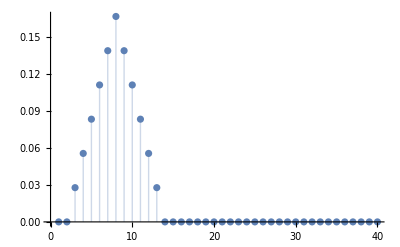

```mathematica
ListPlot[M2[[1]], Filling->Bottom]
```

#### Distribución inicial de probabilidad

Todos parten de la casilla inicial:

```mathematica
α=ConstantArray[0,40]; α[[1]] = 1; α
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

-Graphics-

### Estudio teórico sobre la matriz de transición M

Es regular, por definición, tomando n = 100 (o n = 200 para M),  tenemos M2 > 0

```mathematica
N[MatrixPower[M2,100],3] // MatrixForm
```

(0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025
0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025 | 0.025)

Por el teorema, M tiene distribución límite y es la única distribución estacionaria con todos sus términos estrictamente positivos.

Sin utilizar que M es regular:

Además, como M_ij^n ≃ 0.025 > 0	  ∀i,j , n=200
Todos los estados pertenecen a una misma clase de comunicación.
⟹ La Cadena de Markov es irreducible, sólo tiene una clase de comunicación.

Como además es finita
⟹ Todos sus estados son recurrentes,
y obviamente, la clase es cerrada.

Por el Teorema “Sea (X_n) CMH finita e irreducible, entonces  μ_j = E[  T_j |X_0=j ] < ∞  ∀j, y ( μ_1, μ_2,..., μ_N) es la única distribución estacionaria positiva de la cadena”:
⟹ Las esperanzas son finitas.

Para estudiar la periodicidad, como todos los estados de la misma clase tienen el mismo periodo, basta estudiar la de una casilla.
La primera casilla: d(0) := mcd( n>0 : M_00^n > 0 )
Como para n=11 y n=13 las probabilidades son positivas, d(i)=1 ∀i, y como es irreducible:
⟹ La cadena es aperiódica.

Por definición, como la CM es irreducible, aperiódica y  μ_j = E[  T_j |X_0=j ] < +∞ ∀j:
⟹ La cadena es ergódica.

Por el Teorema II:
La CM es ergódica ⟺ M es regular.

```mathematica
Manipulate[ListPlot[MatrixPower[M,y][[1]], PlotRange->{{0,41},{0,0.17}}, Filling->Bottom], {y,11,13,2}]
```

## ⟹ Sabemos que existe la distribución límite

### Estudio numérico sobre la matriz de transición M

Veamos numéricamente cómo la distribución inicial evoluciona.
En el artículo las primeras distribuciones tienen forma triangular con picos en la séptima casilla, y van reduciéndose hasta valores próximos a 1/40

```mathematica
α.M
Manipulate[ListPlot[α.MatrixPower[M,y], PlotRange->{{0,40},{0,0.17}},Filling->Bottom], {y,1,100,1}]
Manipulate[ListPlot[α.MatrixPower[M2,y], PlotRange->{{0,40},{0,0.17}}, Filling->Bottom], {y,1,100,1}]
```

{0,1/6,1/6,1/6,1/6,1/6,1/6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

-Graphics-

#### Autovalores y autovectores, numéricamente:

```mathematica
Eigensystem[N[Transpose[M]],2]
```

{{1.,0.822277+0.503892 ⅈ},{{0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ},{0.140881+0.0717822 ⅈ,0.150375+0.0488599 ⅈ,0.156167+0.0247345 ⅈ,0.158114+0. ⅈ,0.156167-0.0247345 ⅈ,0.150375-0.0488599 ⅈ,0.140881-0.0717822 ⅈ,0.127917-0.092937 ⅈ,0.111803-0.111803 ⅈ,0.092937-0.127917 ⅈ,0.0717822-0.140881 ⅈ,0.0488599-0.150375 ⅈ,0.0247345-0.156167 ⅈ,-1.55956×10^-16-0.158114 ⅈ,-0.0247345-0.156167 ⅈ,-0.0488599-0.150375 ⅈ,-0.0717822-0.140881 ⅈ,-0.092937-0.127917 ⅈ,-0.111803-0.111803 ⅈ,-0.127917-0.092937 ⅈ,-0.140881-0.0717822 ⅈ,-0.150375-0.0488599 ⅈ,-0.156167-0.0247345 ⅈ,-0.158114-2.8935×10^-16 ⅈ,-0.156167+0.0247345 ⅈ,-0.150375+0.0488599 ⅈ,-0.140881+0.0717822 ⅈ,-0.127917+0.092937 ⅈ,-0.111803+0.111803 ⅈ,-0.092937+0.127917 ⅈ,-0.0717822+0.140881 ⅈ,-0.0488599+0.150375 ⅈ,-0.0247345+0.156167 ⅈ,1.7242×10^-16+0.158114 ⅈ,0.0247345+0.156167 ⅈ,0.0488599+0.150375 ⅈ,0.0717822+0.140881 ⅈ,0.092937+0.127917 ⅈ,0.111803+0.111803 ⅈ,0.127917+0.092937 ⅈ}}}

El artículo indica que el segundo autovalor más grande tiene un valor absoluto de 0.964

```mathematica
0.8222767348221041+0.5038918311681153 ⅈ // Abs
```

0.964389

Debemos dividir por su suma total el autovector del autovalor 1, para que sea una distribución de probabilidad:

```mathematica
Eigenvectors[N[Transpose[M]],1][[1]]/Total[Eigenvectors[N[Transpose[M]],1][[1]]]
```

{0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ}

Corresponde con las filas de la matriz anterior, como indica el teorema de la distribución límite.

#### Autovalores y autovectores:

```mathematica
Eigensystem[Transpose[M],2]
```

{{1,1/6 Root[1+8 #1+36 #1^2+32 #1^3+109 #1^4+912 #1^5+4012 #1^6+9156 #1^7+11911 #1^8+9800 #1^9+5452 #1^10+1856 #1^11+209 #1^12-20 #1^13+10 #1^14-4 #1^15+#1^16&,16]},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{(119669820672551011296989+18+41004635919291805107055 Root[1+8 #1+36 #1^2+12+10 #1^14-4 #1^15+#1^16&,16]^15)/255220368388398881929781,1/255220368388398881929781,(24+1-54972484696823233835511 Root[1&,16]^15)/255220368388398881929781,(26951959353431854329+16+1)/27440099815976656481,32,1/2519781,(84236522595806273681672+16+62469758190110867296024 1^15)/255220368388398881929781,1/255220368388398881929781,1}}}
 |  |  |  |

Obtenemos el autovector distribución de probabilidad:

```mathematica
est=Eigenvectors[Transpose[M],1][[1]]/Total[Eigenvectors[Transpose[M],1][[1]]]
```

{1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40}

Tal como se veía numéricamente, la probabilidad de caer en una de las 40 casillas se distribuye uniformemente a lo largo del tiempo.

Vemos también que es distribución estacionaria, con todos los elementos estrictamente positivos:

```mathematica
est.M
```

{1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40}

# Monopoly Revisited

En esta versión daremos cuenta de las reglas relacionadas con la cárcel.
La cárcel ahora serán 3 casillas:

VE A LA CÁRCEL : primer turno en la cárcel

SIGUE EN LA CÁRCEL : segundo turno en la cárcel

SAL DE LA CÁRCEL / SOLO VISITAS : tercer turno en la cárcel o de paso como una casilla normal

Las reglas que afectan para enviarte a la cárcel son 3:

Tirar 3 dobles seguidos

Caer en la casilla VE A LA CÁRCEL

Sacar una tarjeta de SUERTE o CAJA DE COMUNIDAD que te envía a la cárcel

Para salir de la cárcel no contamos ni el pagar 50€, ni las tarjetas de suerte, sólo el sacar dobles o esperar.

-Graphics-

## Tres dobles consecutivos

Empezamos redefiniendo la variable aleatoria para tener en cuenta múltiples tiradas:
X_n : Variable aleatoria que indica la casilla más lejana donde llegamos en el lanzamiento n (la última tras repetir lanzamientos).

Partimos de la versión anterior, con M la matriz de tirar un único dado.

```mathematica
(* Tirada de un dado *)
M = Table[ If[  1 <= Mod[j-i, 40]  ≤ 6,1/6, 0] , {i,40},{j,40}] ;
```

La transformamos al tiro de dos dados:

```mathematica
(* Tirada de dos dados *)
M = MatrixPower[M,2];
```

Vemos cómo actúa el primer lanzamiento:

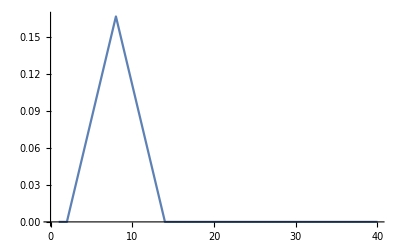

```mathematica
ListPlot[M[[1]], Joined->True]
```

## Tres dobles consecutivos

## Dobles en la primera tirada

La probabilidad de sacar dobles en la primera tirada es 1/36 para cada valor en el dado {1,2,3,4,5,6}.
Debemos distribuir esa probabilidad en una segunda tirada de los dados.
Bastará con definir el vector inicial y multiplicarlo por M, la matriz de transición de tirar 2 dados.
Lo hacemos con la tirada desde la casilla inicial, pues la CM será homogénea y moviendo (módulo  40) una posición a la derecha por cada fila, tendremos la matriz.

En la primera tirada, sacar un doble te deja en una de estas casillas: {2,4,6,8,10,12} con la misma probabilidad.

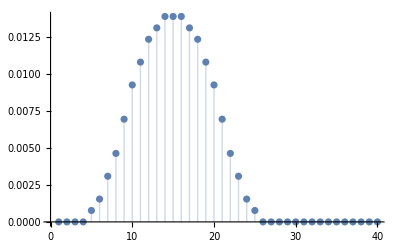

```mathematica
(* Cómo se distribuye la probabilidad de sacar dobles tras la siguiente tirada *)
diceS1 = {0,0,1/36,0,1/36,0,1/36,0,1/36,0,1/36,0,1/36,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
diceS1.M;
ListPlot[diceS1.M, Filling->Bottom]
```

```mathematica
(* Matriz probabilidades de dobles del primer lanzamiento *)
( DICES1 = Table[  diceS1[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  )// MatrixForm;
```

```mathematica
(* Matriz probabilidades de dobles del primer lanzamiento distribuidas en el segundo lanzamiento *)
( DICES1M = Table[  (diceS1.M)[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  )// MatrixForm;
```

## Tres dobles consecutivos

## Dobles en la segunda tirada

Del mismo modo, calculamos el vector de probabilidades de sacar un segundo doble en la primera tirada.
Utilizamos una tabla donde nos indica en qué casilla acabamos si:
· Partimos desde la casilla indicada en las filas.
· Sacamos dobles del valor en las columnas.

# | 1 | 2 | 3 | 4 | 5 | 6
2 | 4 | 6 | 8 | 10 | 12 | 14
4 | 6 | 8 | 10 | 12 | 14 | 16
6 | 8 | 10 | 12 | 14 | 16 | 18
8 | 10 | 12 | 14 | 16 | 18 | 20
10 | 12 | 14 | 16 | 18 | 20 | 22
12 | 14 | 16 | 18 | 20 | 22 | 24

Y la probabilidad de sacar dobles en dos lanzamientos independientes es 1/36 x 1/36=1/1296

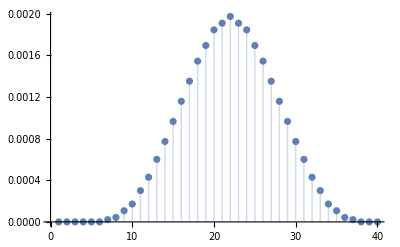

```mathematica
diceS2 = {0,0,0,0,1/1296,0,2/1296,0,3/1296,0,4/1296,0,5/1296,0,6/1296,0,5/1296,0,4/1296,0,3/1296,0,2/1296,0,1/1296,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
diceS2.M;
ListPlot[diceS2.M, Filling->Bottom]
```

De ese vector inicial sacamos las matrices correspondientes:

```mathematica
(* Matriz probabilidades de dobles del segundo lanzamiento *)
( DICES2 = Table[  diceS2[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  ) // MatrixForm;
(* Matriz probabilidades de dobles del segundo lanzamiento distribuidas en el tercer lanzamiento *)
( DICES2M = Table[  (diceS2.M)[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  ) // MatrixForm;
```

## Tres dobles consecutivos

## Dobles en la tercera tirada

Del mismo modo, obtenemos las probabilidades de acabar en cada casilla tras un tercer doble.
Pero no calculamos cómo se reparte esa probabilidad en un cuarto lanzamiento, pues vamos directamente  a la cárcel.
Vemos que se puede llegar hasta la casilla 36, al lanzar tres veces seguidas 6 dobles.

```mathematica
diceS3 = {0,0,0,0,0,0,1/46656,0,3/46656,0,6/46656,0,(1+2+3+4)/46656,0,(5+4+3+2+1)/46656,0,(6+5+4+3+2+1)/46656,0,(5+6+5+4+3+2)/46656,0,(4+5+6+5+4+3)/46656,0,(3+4+5+6+5+4)/46656,0,(2+3+4+5+6+5)/46656,0,(1+2+3+4+5+6)/46656,0,(1+2+3+4+5)/46656,0,(1+2+3+4)/46656,0,6/46656,0,3/46656,0,1/46656,0,0,0};
```

Comprobamos que la suma de la probabilidad debe ser  1/216, las probabilidad de 3 dobles seguidos (6x6x6=216):

```mathematica
Total[diceS3]
```

1/216

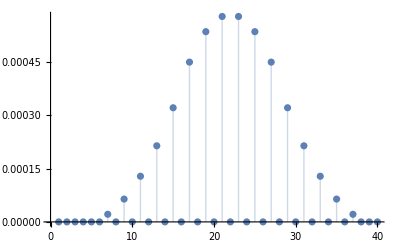

```mathematica
ListPlot[diceS3, Filling->Bottom]
```

```mathematica
(* Matriz probabilidades de dobles del tercer lanzamiento *)
( DICES3 = Table[  diceS3[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  ) // MatrixForm;
```

## Tres dobles consecutivos

## La nueva matriz de transición

La nueva matriz de transición con la regla de los tres dobles se calcula como sigue:

Matriz de transición  = 	  Tirar 2 dados (M)
					- Prob. dobles
					+ Prob. distribuida en segundo lanzamiento
					- Prob. dobles en segundo lanzamiento
					+ Prob. distribuida en tercer lanzamiento
					- Prob. dobles en tercer lanzamiento
						# Añadir probabilidad dobles en tercer lanzamiento a la cárcel

```mathematica
( P = M - DICES1 + DICES1M  - DICES2 + DICES2M - DICES3 ) // MatrixForm;
```

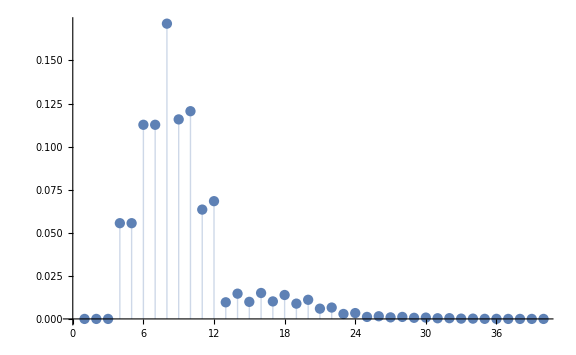

```mathematica
Show[ListPlot[P[[1]], Filling->Bottom] ,ImageSize->Large]
```

Comparamos con el artículo original:

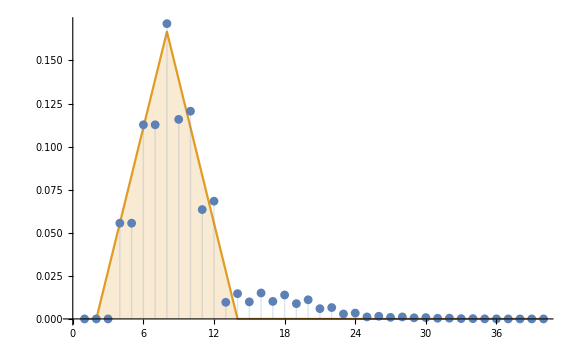

```mathematica
Show[ListPlot[{P[[1]],M[[1]]}, Filling->Bottom, Joined->{False,True}] ,ImageSize->Large]
```

-Graphics-

## Nueva cárcel

Añadimos las 2 casillas virtuales al tablero.
En la matriz de transición son 2 filas y 2 columnas al final.

```mathematica
zeroes = ConstantArray[0,40];
( P=Transpose[Insert[Transpose[P],zeroes,41]] );
( P=Transpose[Insert[Transpose[P],zeroes,42]] );
zeroes = ConstantArray[0,42];
( P = Insert[P,zeroes, 41]);
( P = Insert[P,zeroes, 42]) //MatrixForm;
```

```mathematica
P // MatrixForm
```

(0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0
1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 0 | 0
1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 0 | 0
1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 0 | 0
1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 0 | 0
5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 0 | 0
1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 0 | 0
1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 0 | 0
5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 0 | 0
1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 0 | 0
7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 0 | 0
1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 0 | 0
1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 0 | 0
79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 0 | 0
67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 0 | 0
77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 0 | 0
139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 0 | 0
259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 0 | 0
23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 0 | 0
1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 0 | 0
79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 0 | 0
13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 0 | 0
77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 0 | 0
19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 0 | 0
25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 0 | 0
797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 0 | 0
185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 0 | 0
703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 0 | 0
2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 0 | 0
3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 0 | 0
73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 0 | 0
73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 0 | 0
1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0
1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Nueva cárcel

Sumamos las probabilidades de ir a la carcel (casilla 41) si lanzamos tres dobles o si caemos en la casilla VE A LA CÁRCEL:
En la casilla VE A LA CÁRCEL (31) ya no se lanzan dados, probabilidades a 0, excepto la de ir a la cárcel.

```mathematica
(* GO TO JAIL if 3 consecutive doubles or GOTOJAIL *)
For[i=1, i≤ 40,i++,
P[[i,41]] += 1/216 + P[[i,31]];
P[[i,31]] = 0; P[[31,i]] = 0;
]
P[[31,41]]=1;
```

## Escapar de la nueva cárcel

Podemos salir de la cárcel si lanzamos dobles.
Virtualmente estamos en la casilla de CÁRCEL, y las probabilidades de alcanzar otras casillas son las mismas.
Según las reglas del juego, sólo se lanzan los dados una vez, aunque se hayan obtenido dobles.

```mathematica
(* KEEP ON JAIL or GET OUT OF JAIL if a double *)
outofJail =  {0,0,0,0,0,0,0,0,0,0,0,0,1/36,0,1/36,0,1/36,0,1/36,0,1/36,0,1/36,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
P[[41]] = outofJail; P[[42]] = outofJail;
```

Si no se sacan dobles, se pasa a la siguiente casilla virtual (41 -> 42, 42 -> 11).

```mathematica
(* No doubles *) 
P[[41, 42]] = 1-6/36; P[[42, 11]]=1-6/36;
```

## Tarjetas de suerte y Cajas de la comunidad

Una vez tenemos todas las reglas que afectan a los dados (entrar o salir de la cárcel), veamos las tarjetas de suerte.

-Graphics-

Supondremos que hay una tarjeta de ir a la carcel en cada montón de 16 cartas de suerte o comunidad, y que tras sacarla, el montón se baraja de nuevo.
La probabilidad se distribuye añadiendo un 1/16 de la probabilidad de caer en una casilla de suerte o comunidad, a la de ir a la cárcel,
y restando ese 1/16 de la probabilidad original.

```mathematica
(* Chance card & Community chest: GO TO JAIL 1/16 *)
For[i=1, i≤ 40,i++,
P[[i,41]] += P[[i,8]] *(1/16);    P[[i,8]]  -=P[[i,8]] *(1/16);
P[[i,41]] += P[[i,18]] *(1/16);  P[[i,18]]-=P[[i,18]] *(1/16);
P[[i,41]] += P[[i,23]] *(1/16);  P[[i,23]]-= P[[i,23]] *(1/16);
P[[i,41]] += P[[i,34]] *(1/16);  P[[i,34]]-= P[[i,34]] *(1/16);
P[[i,41]] += P[[i,37]] *(1/16);  P[[i,37]]-=P[[i,37]] *(1/16);
]
```

## La nueva matriz de transición

Comprobamos que es una matriz estocástica:

```mathematica
For[i=1, i≤ 42,i++, If[Total[P[[i]]]≠1, Print["Error en fila ", i, " : ", Total[P[[i]]]]] ]
```

```mathematica
P // MatrixForm
```

(0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 0 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 29/1728 | 0
0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 0 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 35/2592 | 0
0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 0 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 1699/124416 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 0 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 3959/373248 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 0 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 3931/373248 | 0
1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 0 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1439/186624 | 0
1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 0 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 4027/373248 | 0
1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 0 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 2431/186624 | 0
1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 0 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 2947/186624 | 0
5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 0 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 7289/373248 | 0
1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 0 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1379/62208 | 0
1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 0 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1133/41472 | 0
5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 0 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 1555/62208 | 0
1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 0 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 11239/373248 | 0
7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 0 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 9847/373248 | 0
1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 0 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1951/62208 | 0
1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 0 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 8525/373248 | 0
79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 0 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 10333/373248 | 0
67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 0 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 25/1296 | 0
77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 0 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 14549/186624 | 0
139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 0 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 13007/186624 | 0
259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 0 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 47317/373248 | 0
23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 0 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 7801/62208 | 0
1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 0 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 11255/62208 | 0
79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 0 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 977/7776 | 0
13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 0 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 24071/186624 | 0
77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 28105/373248 | 0
19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 1039/13824 | 0
25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 815/41472 | 0
797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 7247/373248 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 289/23328 | 0
2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 95/10368 | 0
3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 275/31104 | 0
73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 541/93312 | 0
73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 2063/373248 | 0
1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 0 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1171/124416 | 0
1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 0 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 383/41472 | 0
0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 0 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 4891/373248 | 0
0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 0 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 1219/93312 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## ¡P NO ES REGULAR!

Para potencias 100 y 101, los ceros de P^n y P^(n+1) mantienen los ceros en las mismas posiciones, la columna 31, correspondiente a la casilla VE A LA CÁRCEL, en la que nunca llegamos es estar realmente.

```mathematica
N[MatrixPower[P,100],3] // MatrixForm 
N[MatrixPower[P,101],3] // MatrixForm
```

(0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305)

(0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305)

## Quitando la casilla inalcanzable

Como se menciona en el artículo y se observa en P, la casilla VE A LA CÁRCEL no se puede alcanzar.
Esto complica un estudio teórico sobre la matriz, pues no es regular.
Sería además no irreducible, con dos clases de comunicación, una transitoria (VE A LA CÁRCEL) y la otra recurrente (el resto de casillas).

Pero como nosotros hemos creado la matriz, no nos viene dada, podemos adaptarlo como mejor convenga al modelo.

VE A LA CÁRCEL se vería como un nodo aislado, podemos eliminar su fila y columna, y el modelo seguiría representando el mismo juego.

-Graphics-

Llamamos Q a la nueva matriz de transición sin la casilla VE A LA CÁRCEL

```mathematica
( Q = Drop[Drop[P,0,{31}],{31}] ) // MatrixForm
```

(0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 29/1728 | 0
0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 35/2592 | 0
0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 1699/124416 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 3959/373248 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 3931/373248 | 0
1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1439/186624 | 0
1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 4027/373248 | 0
1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 2431/186624 | 0
1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 2947/186624 | 0
5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 7289/373248 | 0
1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1379/62208 | 0
1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1133/41472 | 0
5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 1555/62208 | 0
1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 11239/373248 | 0
7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 9847/373248 | 0
1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1951/62208 | 0
1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 8525/373248 | 0
79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 10333/373248 | 0
67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 25/1296 | 0
77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 14549/186624 | 0
139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 13007/186624 | 0
259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 47317/373248 | 0
23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 7801/62208 | 0
1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 11255/62208 | 0
79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 977/7776 | 0
13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 24071/186624 | 0
77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 28105/373248 | 0
19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 1039/13824 | 0
25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 815/41472 | 0
797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 7247/373248 | 0
703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 289/23328 | 0
2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 95/10368 | 0
3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 275/31104 | 0
73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 541/93312 | 0
73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 2063/373248 | 0
1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1171/124416 | 0
1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 383/41472 | 0
0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 4891/373248 | 0
0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 1219/93312 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Comprobamos que sigue siendo una matriz estocástica:s

```mathematica
For[i=1, i≤ 41,i++, If[Total[Q[[i]]]≠1, Print["Error en fila ", i, " : ", Total[Q[[i]]]]] ]
```

## ¡Q SÍ ES REGULAR!

Como Q sí es regular, podemos realizar las mismas deducciones que hicimos sobre M, y por tanto,
existe distribución límite.

```mathematica
N[MatrixPower[Q,100],3] // MatrixForm
```

(0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305
0.0219 | 0.0214 | 0.0222 | 0.0218 | 0.0215 | 0.0214 | 0.0214 | 0.02 | 0.0215 | 0.0215 | 0.0468 | 0.0214 | 0.0232 | 0.0227 | 0.0244 | 0.0242 | 0.0261 | 0.0244 | 0.0267 | 0.0256 | 0.0263 | 0.0252 | 0.0244 | 0.0248 | 0.0248 | 0.0253 | 0.0251 | 0.0254 | 0.0251 | 0.0252 | 0.025 | 0.0249 | 0.0221 | 0.0236 | 0.0222 | 0.0206 | 0.0204 | 0.0215 | 0.021 | 0.0366 | 0.0305)

```mathematica
aux = N[MatrixPower[Q,100],10];
For[i=1, i≤ 41,i++,
For[j=1, j≤ 41,j++,
If[aux[[i,j]] <0.00001, Print["Cero en ", i, " : ", j]] 
]
]
```

## La distribución límite

```mathematica
Eigensystem[N[Transpose[Q]], 2]
```

{{1.,0.251911+0.781808 ⅈ},{{-0.13749+0. ⅈ,-0.134381+0. ⅈ,-0.139935+0. ⅈ,-0.137151+0. ⅈ,-0.135388+0. ⅈ,-0.134665+0. ⅈ,-0.134534+0. ⅈ,-0.126022+0. ⅈ,-0.13503+0. ⅈ,-0.135297+0. ⅈ,-0.294703+0. ⅈ,-0.134737+0. ⅈ,-0.145773+0. ⅈ,-0.142666+0. ⅈ,-0.153702+0. ⅈ,-0.152013+0. ⅈ,-0.164071+0. ⅈ,-0.153637+0. ⅈ,-0.168072+0. ⅈ,-0.160958+0. ⅈ,-0.16537+0. ⅈ,-0.158699+0. ⅈ,-0.153424+0. ⅈ,-0.156048+0. ⅈ,-0.155933+0. ⅈ,-0.159321+0. ⅈ,-0.158119+0. ⅈ,-0.159666+0. ⅈ,-0.157713+0. ⅈ,-0.158244+0. ⅈ,-0.1572+0. ⅈ,-0.156802+0. ⅈ,-0.139154+0. ⅈ,-0.148513+0. ⅈ,-0.139638+0. ⅈ,-0.129898+0. ⅈ,-0.128666+0. ⅈ,-0.135189+0. ⅈ,-0.132263+0. ⅈ,-0.23008+0. ⅈ,-0.191733+0. ⅈ},{-0.0494336-0.134653 ⅈ,-0.0693008-0.122146 ⅈ,-0.0858892-0.117306 ⅈ,-0.101722-0.098493 ⅈ,-0.114046-0.0786457 ⅈ,-0.126577-0.0571141 ⅈ,-0.134451-0.0356201 ⅈ,-0.131796-0.0121246 ⅈ,-0.141716+0.00861863 ⅈ,-0.140148+0.030602 ⅈ,-0.29557+0. ⅈ,-0.122779+0.0712062 ⅈ,-0.113941+0.0820238 ⅈ,-0.0991488+0.115486 ⅈ,-0.0855988+0.121734 ⅈ,-0.0677713+0.150372 ⅈ,-0.0512764+0.151184 ⅈ,-0.0297444+0.162613 ⅈ,-0.0063607+0.158429 ⅈ,0.0203882+0.165488 ⅈ,0.0466436+0.144418 ⅈ,0.0724061+0.144935 ⅈ,0.0904248+0.109674 ⅈ,0.118082+0.111307 ⅈ,0.136338+0.0934623 ⅈ,0.144725+0.0731541 ⅈ,0.155685+0.049058 ⅈ,0.157108+0.0235764 ⅈ,0.160255-0.00344797 ⅈ,0.154922-0.0300928 ⅈ,0.139715-0.0801371 ⅈ,0.127897-0.101393 ⅈ,0.10313-0.102511 ⅈ,0.0908654-0.124654 ⅈ,0.0676956-0.125986 ⅈ,0.0410414-0.1251 ⅈ,0.0186151-0.127159 ⅈ,-0.00561925-0.137514 ⅈ,-0.0289449-0.132853 ⅈ,0.15735-0.0522045 ⅈ,-0.0014522-0.168188 ⅈ}}}

{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,0.0267124,0.0255818,0.0262831,0.0252228,0.0243843,0.0248014,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731}

{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,0.0267124,0.0255818,0.0262831,0.0252228,0.0243843,0.0248014,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731}

1.

1.9214×10^-16

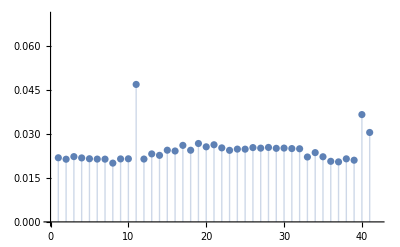

```mathematica
est = Re[Eigenvectors[N[Transpose[Q]],1][[1]]/Total[Eigenvectors[N[Transpose[Q]],1][[1]]] ]
est.Q
Total[est]
Norm[est-est.Q]
(* For[i=1, i≤ 40, i++, If[GreaterThan[0][est[[i]]], Print["ok"], Print["Not ok"]]] *)
ListPlot[est, PlotRange->{{0,42},{0,0.07}},Filling->Bottom]
```

-Graphics-

## La distribución límite a partir de potencias de Q

A partir de la distribución inicial y viendo cómo evoluciona

```mathematica
α=ConstantArray[0,41]; α[[1]] = 1; α
Manipulate[ListPlot[α.MatrixPower[Q,y], PlotRange->{{0,42},{0,0.07}},Filling->Bottom], {y,1,100,1}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

O según el teorema, tomando una fila cualquiera de Q^n:

```mathematica
Manipulate[ListPlot[MatrixPower[Q,y][[15]], PlotRange->{{0,42},{0,0.07}},Filling->Bottom], {y,1,100,1}]
```

## Comparación con los resultados del artículo

En el artículo calculan la distribución límite a partir de las potencias de la matriz.

No eliminan la casilla de la cárcel.

Calculan la probabilidad de la cárcel como otro subproceso de Markov aparte, pero no indican cómo lo suman a su única casilla de cárcel, ni si incluyen la regla de que se avanzan las casillas del doble obtenido para salir de la cárcel.

En este estudio hay tres casillas de cárcel, y se puede salir sacando dobles o esperando.

Las gráficas muestran varias similitudes, aunque casillas próximas con probabilidades muy distintas en el artículo, en nuestro resultado tienen menor diferencia:

La casilla de salida no presenta la gran diferencia que aparece en el artículo, y tampoco se ve afectada por reglas del juego que le den tal ventaja.

Las casillas finales e iniciales tienen menor probabilidad, aunque no tan dispar entre sí como en el artículo.

Las casillas centrales tras la cárcel tienen mayor probabilidad.

La compañía de electricidad presenta un pico similar en ambas.

La última tarjeta de suerte tiene un valle parecido en ambas.

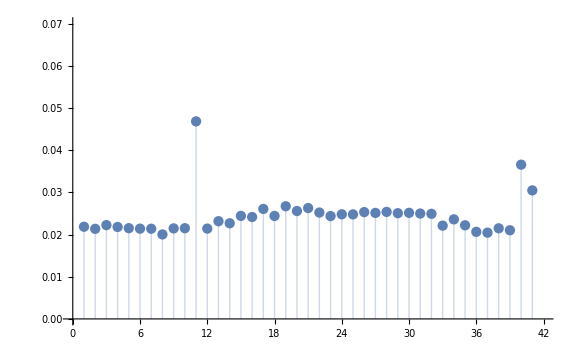

```mathematica
Show[ListPlot[est, PlotRange->{{0,42},{0,0.07}},Filling->Bottom] ,ImageSize->Large]
```

-Graphics-

-Graphics-